## Pendulum swing up & balance, with local linear feedback. Test 3 ways to choose feedback gains (Problem 7.19)

```mathematica
Clear["Global`*"];

ffCalc[n_,τ_]:=Module[{f,θ,θdot,λ,λdot,t,Δt,bcs,eqns,sv,froot,θff0,θdotff0,uff0,θff,θdotff,uff},
Δt=τ/n;
f[{θ_,θdot_,λ_,λdot_}] := {θdot,-Sin[θ]-λ,λdot,-Cos[θ]λ};
bcs={Subscript[θ, 0]==0,Subscript[θdot, 0]==0,Subscript[θ, n]==π,Subscript[θdot, n]==0}; (* hard final constraint *)
eqns=Flatten[Join[bcs,
Table[Thread[{Subscript[θ, i],Subscript[θdot, i],Subscript[λ, i],Subscript[λdot, i]}== {Subscript[θ, i-1],Subscript[θdot, i-1],Subscript[λ, i-1],Subscript[λdot, i-1]}
+Δt/2(f[{Subscript[θ, i-1],Subscript[θdot, i-1],Subscript[λ, i-1],Subscript[λdot, i-1]}]+f[{Subscript[θ, i],Subscript[θdot, i],Subscript[λ, i],Subscript[λdot, i]}])],{i,1,n}]]];
sv=Flatten[Table[{{Subscript[θ, i],0},{Subscript[θdot, i],0},{Subscript[λ, i],0},{Subscript[λdot, i],0}},{i,0,n}],1];
	(* initial guesses = 0, very naive! *)
froot=FindRoot[eqns,sv];

θff0=ListInterpolation[Table[Subscript[θ, i],{i,0,n}]/.froot,{0,τ}];
θdotff0=ListInterpolation[Table[Subscript[θdot, i],{i,0,n}]/.froot,{0,τ}];
uff0=ListInterpolation[Table[-Subscript[λ, i],{i,0,n}]/.froot,{0,τ}];

θff[t_]:=Piecewise[{{θff0[t],0≤t≤τ}},π];
θdotff[t_]:=Piecewise[{{θdotff0[t],0≤t≤τ}},0];
uff[t_]:=Piecewise[{{uff0[t],0≤t≤τ}},0];
{θff,θdotff,uff}]

n=500;  τ=5;τ1=3τ;
{θ0,θdot0,u0}=ffCalc[n,τ];
p0=Plot[{θ0[t],u0[t],π},{t,0,τ1},PlotStyle->{,,Directive[Gray,Dashed,Thin]},Filling->{2->Axis},PlotRange->{-1,4}];
```

Test the approximate solution on the open-loop
 dynamics (integrated at a fine time step)

```mathematica
TestSwingUp[τ1_,uff_]:=Module[{eq,init,θ,θdot,θs,θdots,us,t},
eq={θ'[t]==θdot[t],θdot'[t]==-Sin[θ[t]]+uff[t]};
init={θ[0]==θdot[0]==0};
{θs,θdots}=NDSolveValue[{eq,init},{θ,θdot},{t,0,τ1}];
θs]

θ1=TestSwingUp[τ1,u0];
p1=Plot[{θ1[t],u0[t],π},{t,0,τ1},PlotStyle->{,,Directive[Gray,Dashed,Thin]},PlotRange->{-1,4},Filling->{2->Axis}];
```

InterpolatingFunction::dmval: Input value {5.05981} lies outside the range of data in the interpolating function. Extrapolation will be used.

Show that linear feedback can stabilize against various perturbations.  Use LQR for balance state for everywhere.

```mathematica
TestSwingUpFB[τ_,τ1_,d_,θff_,θdotff_,uff_]:=Module[{eq,init,θ,θdot,t,κ1,κ2,ufb,u,θs,θdots,us},
κ1=κ2=√2+1;  (* lqr for q=r for balancing pendulum *)
ufb[t_]:=Piecewise[{{κ1(θff[t]-θ[t])+κ2 (θdotff[t]-θdot[t]),0≤t≤12.99}},0];
u[t_]:=uff[t]+ufb[t];
eq={θ'[t]==θdot[t],θdot'[t]==-Sin[θ[t]]+u[t]};
init={θ[0]==0,θdot[0]==d};
{θs,θdots}=NDSolveValue[{eq,init},{θ,θdot},{t,0,τ1}];
us[t_]:=Piecewise[{{uff[t]+κ1(θff[t]-θs[t])+κ2 (θdotff[t]-θdots[t]),0≤t≤12.99}},0];
{θs,us}]

d=0.7;
{θ2,u2}=TestSwingUpFB[τ,τ1,d,θ0,θdot0,u0];
p2=Plot[{θ2[t],u2[t],π},{t,0,τ1},PlotStyle->{,,Directive[Gray,Dashed,Thin]},PlotRange->{-1,4},Filling->{2->Axis}];
```

InterpolatingFunction::dmval: Input value {5.02172} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

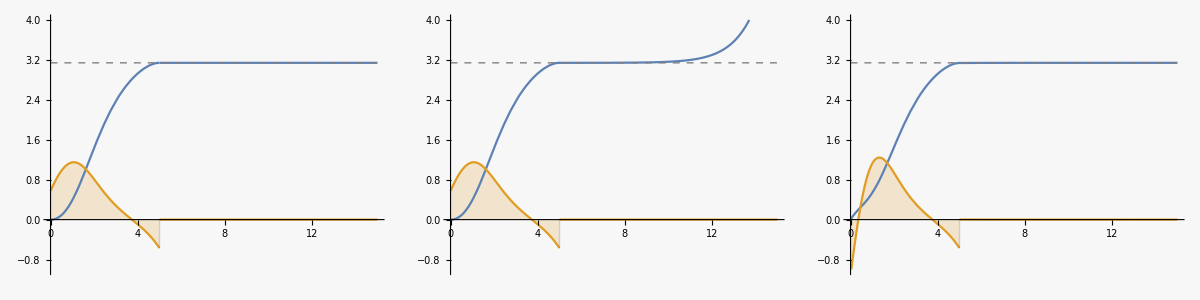

```mathematica
Grid[{{p0,p1,p2}},Spacings->4]
```

Linear feedback:  Quasistationary approximation (Q=R=1)

```mathematica
a=({{0, 1}, {-Cos[θ], 0}});b=({{0}, {1}});s=({{s11, s12}, {s12, s22}});q=({{Q, 0}, {0, Q}});r={{R}};
ric=aᵀ.s+s.a-s.b.Inverse[r].bᵀ.s+q;MatrixForm[ric]
```

(Q-s12^2/R-2 s12 Cos[θ] | s11-(s12 s22)/R-s22 Cos[θ]
s11-(s12 s22)/R-s22 Cos[θ] | Q+2 s12-s22^2/R)

```mathematica
r11=ric[[1,1]]/.{Q->1,R->1};r12=ric[[1,2]]/.{Q->1,R->1};r22=ric[[2,2]]/.{Q->1,R->1};
sol=Solve[{r11==0,r12==0,r22==0},{s12,s22,s11}][[4]]
```

{s12→-Cos[θ]+√(1+Cos[θ]^2),s22→√(1-2 Cos[θ]+2 √(1+Cos[θ]^2)),s11→√(1+Cos[θ]^2) √(1-2 Cos[θ]+2 √(1+Cos[θ]^2))}

```mathematica
{κ1a,κ2a}={s12,s22}/.sol
```

{-Cos[θ]+√(1+Cos[θ]^2),√(1-2 Cos[θ]+2 √(1+Cos[θ]^2))}

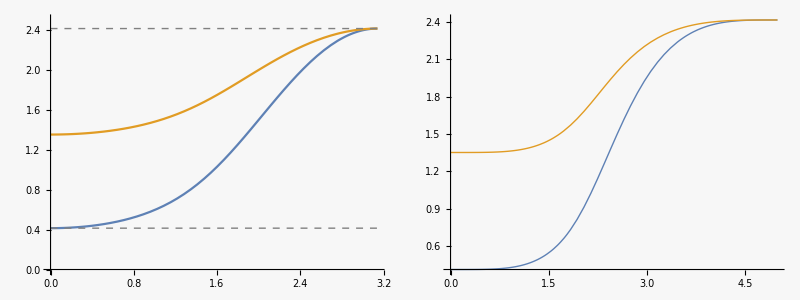

```mathematica
Grid[{{Plot[{κ1a,κ2a,√2+1,√2-1},{θ,0,π},PlotRange->{0,2.5},PlotStyle->{,,Directive[Gray,Dashed,Thin],Directive[Gray,Dashed,Thin]}],
Plot[{κ1a/.θ->θ0[t],κ2a/.θ->θ0[t]},{t,0,τ}]}},Spacings->4]
```

InterpolatingFunction::dmval: Input value {5.02202} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

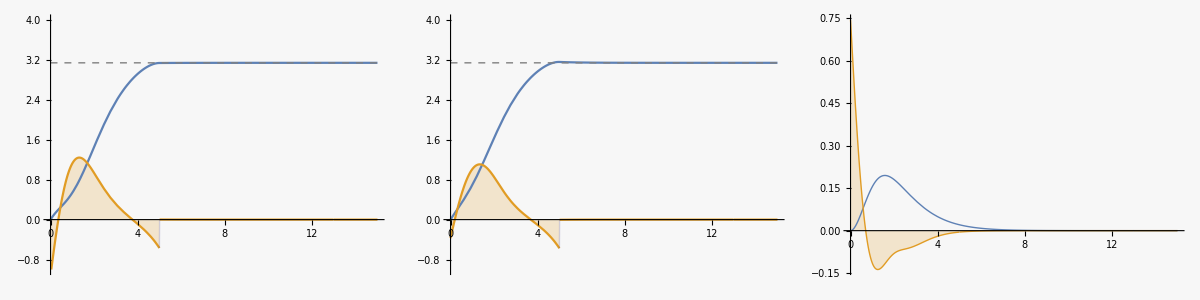

```mathematica
TestSwingUpFBqs[τ_,τ1_,d_,θff_,θdotff_,uff_]:=Module[{eq,init,θ,θdot,t,ufb,u,κ1,κ2,θs,θdots,us,ufbs},
κ1[t_]:=-Cos[θ]+√(1+Cos[θ]^2)/.θ->θff[t];
κ2[t_]:=√(1-2 Cos[θ]+2 √(1+Cos[θ]^2))/.θ->θff[t];
ufb[t_]:=Piecewise[{{κ1[t](θff[t]-θ[t])+κ2[t] (θdotff[t]-θdot[t]),0≤t≤12.99}},0];
u[t_]:=uff[t]+ufb[t];
eq={θ'[t]==θdot[t],θdot'[t]==-Sin[θ[t]]+u[t]};
init={θ[0]==0,θdot[0]==d};
{θs,θdots}=NDSolveValue[{eq,init},{θ,θdot},{t,0,τ1}];
ufbs[t_]:=Piecewise[{{κ1[t](θff[t]-θs[t])+κ2[t] (θdotff[t]-θdots[t]),0≤t≤12.99}},0];
us[t_]:=uff[t]+ufbs[t];{θs,us}]
d=0.7;
{θ3,u3}=TestSwingUpFBqs[τ,τ1,d,θ0,θdot0,u0];
p3=Plot[{θ3[t],u3[t],π},{t,0,τ1},PlotStyle->{,,Directive[Gray,Dashed,Thin]},PlotRange->{-1,4},Filling->{2->Axis}];
p4=Plot[{θ3[t]-θ2[t],u3[t]-u2[t]},{t,0,τ1},PlotRange->All,Filling->{2->Axis}];
Grid[{{p2,p3,p4}},Spacings->4]
```

```mathematica
κ1a
```

-Cos[θ]+√(1+Cos[θ]^2)

Linear feedback:  solve the Riccati equations exactly (for Q=R=1).  Start by solving Riccati eq.

```mathematica
{κ1b,κ2b}={κ1a,κ2a}/.θ->π//FullSimplify
```

{1+√2,1+√2}

```mathematica
{s11end,s12end,s22end}={s11,s12,s22}/.sol/.θ->π//FullSimplify
```

{2+√2,1+√2,1+√2}

General::munfl: (8.9003×10^-308)/7 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (8.9003×10^-308)/6 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (8.9003×10^-308)/5 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

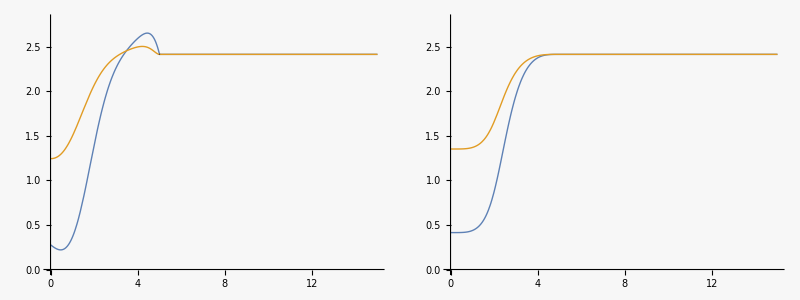

```mathematica
eqr={s11'[t]+1-s12[t]^2-2 s12[t] Cos[θ0[t]]==0,s12'[t]+1+s11[t]-s12[t] s22[t]-s22[t] Cos[θ0[t]]==0,s22'[t]+1+2 s12[t]-s22[t]^2==0};
initr={s11[τ]==s11end,s12[τ]==s12end,s22[τ]==s22end};
{s11s,s12s,s22s}=NDSolveValue[{eqr,initr},{s11,s12,s22},{t,τ,0}];
κopt1[t_]:=s12s[t];κopt2[t_]:=s22s[t];

κopt1a[t_]:=Piecewise[{{κopt1[t],0≤t≤τ}},κ1b]
κopt2a[t_]:=Piecewise[{{κopt2[t],0≤t≤τ}},κ2b];
Grid[{{Plot[{κopt1a[t],κopt2a[t]},{t,0,τ1},PlotRange->{0,2.8}],
Plot[{κ1a/.θ->θ0[t],κ2a/.θ->θ0[t]},{t,0,τ1},PlotRange->{0,2.8}]}},Spacings->4]
```

InterpolatingFunction::dmval: Input value {5.06971} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

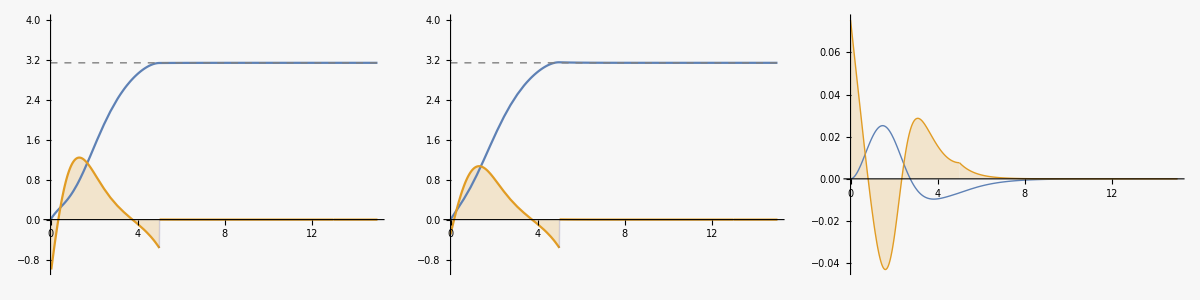

```mathematica
TestSwingUpFBopt[τ_,τ1_,d_,θff_,θdotff_,uff_,κ1_,κ2_]:=Module[{eq,init,θ,θdot,t,ufb,u,θs,θdots,us,ufbs},
(* lqr for q=r, quasistationary approximation *)
ufb[t_]:=Piecewise[{{κ1[t](θff[t]-θ[t])+κ2[t] (θdotff[t]-θdot[t]),0≤t≤12.99}},0];
u[t_]:=uff[t]+ufb[t];
eq={θ'[t]==θdot[t],θdot'[t]==-Sin[θ[t]]+u[t]};
init={θ[0]==0,θdot[0]==d};
{θs,θdots}=NDSolveValue[{eq,init},{θ,θdot},{t,0,τ1}];
ufbs[t_]:=Piecewise[{{κ1[t](θff[t]-θs[t])+κ2[t] (θdotff[t]-θdots[t]),0≤t≤12.99}},0];
us[t_]:=uff[t]+ufbs[t];{θs,us}]
d=0.7;
{θ4,u4}=TestSwingUpFBopt[τ,τ1,d,θ0,θdot0,u0,κopt1a,κopt2a];
p5=Plot[{θ4[t],u4[t],π},{t,0,τ1},PlotStyle->{,,Directive[Gray,Dashed,Thin]},PlotRange->{-1,4},Filling->{2->Axis}];
p6=Plot[{θ4[t]-θ3[t],u4[t]-u3[t]},{t,0,τ1},PlotRange->All,Filling->{2->Axis}];
Grid[{{p2,p5,p6}},Spacings->4]
```

Export data

```mathematica
dt=0.05;
datkappa=Table[{κ1a/.θ->θ0[t],κ2a/.θ->θ0[t],κopt1a[t],κopt2a[t]},{t,0,τ1,dt}]//N;
dat=Table[Through[{θ0,u0,θ1,θ2,u2,θ3,u3,θ4,u4}[t]],{t,0,τ1,dt}]//N;
(* 
SetDirectory[NotebookDirectory[]];
Export["pendulumFBk.dat", datkappa];Export["pendulumFB.dat", dat]; 
*)
```